```mathematica
Quit[]
```

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX` (* Package to make plots with LaTeX fonts *)
```

# Matter Power Spectrum: n_s

## Data

```mathematica
Pkns=Partition[Import["Data_Pk_ns.txt","Data"],500];
```

```mathematica
(* Power spectrum for wCDM from GA *)
Pw[k_,w_]:=(2.5239506940685576*^6 k^0.9645201679721765 (1+0.7106356245167889 w^3+1.8801896647991612 w^4+0.939216799027307 w^5))/(√(1+1395.2489187744666 k^1.4917653903428132+2.3729066856033597*^7 k^4.027553399922359+1.1994340119292421*^9 k^6.0600043498512886+7.611601220332279*^8 k^7.284778673036612))
```

```mathematica
ns=0.965;
S[s_]:=3*10^6*(1+s) (* Shift factor *)
Psup[k_,s_]:=S[s]*k^ns; (* Primordial spectrum *)
Psub[k_,w_]:=Pw[k,w] (* wCDM P(k,w) *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(k-k0)/β)); (* Transition function *)
P[k_,w_,k0_,β_,s_]:=(1-σ[k,k0,β])Psup[k,s]+σ[k,k0,β]*Psub[k,w] (* Total spectrum *)
```

## Comparison

```mathematica
(* Accuracy for each dataset *)
χ2ns0.b496[w_,k0_,β_,s_]:=Mean[Table[Abs[Pkns[[1]]⟦i,2⟧-P[Pkns[[1]]⟦i,1⟧,w,k0,β,s]]/(Pkns[[1]]⟦i,2⟧)*100,{i,1,Length[Pkns[[1]]]}]]
χ2ns0.b49625[w_,k0_,β_,s_]:=Mean[Table[Abs[Pkns[[2]]⟦i,2⟧-P[Pkns[[2]]⟦i,1⟧,w,k0,β,s]]/(Pkns[[2]]⟦i,2⟧)*100,{i,1,Length[Pkns[[2]]]}]]
χ2ns0.b4965[w_,k0_,β_,s_]:=Mean[Table[Abs[Pkns[[3]]⟦i,2⟧-P[Pkns[[3]]⟦i,1⟧,w,k0,β,s]]/(Pkns[[3]]⟦i,2⟧)*100,{i,1,Length[Pkns[[3]]]}]]
χ2ns0.b49675[w_,k0_,β_,s_]:=Mean[Table[Abs[Pkns[[4]]⟦i,2⟧-P[Pkns[[4]]⟦i,1⟧,w,k0,β,s]]/(Pkns[[4]]⟦i,2⟧)*100,{i,1,Length[Pkns[[4]]]}]]
χ2ns0.b497[w_,k0_,β_,s_]:=Mean[Table[Abs[Pkns[[5]]⟦i,2⟧-P[Pkns[[5]]⟦i,1⟧,w,k0,β,s]]/(Pkns[[5]]⟦i,2⟧)*100,{i,1,Length[Pkns[[5]]]}]]
```

```mathematica
(* Compute the most accurate set of parameters *)
Parns0.b496=FindMinimum[χ2ns0.b496[w,k0,β,s],{{w,1,0},{k0,0.000001,0.001},{β,0.01,0.001},{s,0,1}}]
Parns0.b49625=FindMinimum[χ2ns0.b49625[w,k0,β,s],{{w,0.2,0.4},{k0,0.0001,0.001},{β,0.01,0.001},{s,0,0.1}}]
Parns0.b4965=FindMinimum[χ2ns0.b4965[w,k0,β,s],{{w,1,0},{k0,0.0001,0.001},{β,0.0001,0.001},{s,0,1}}]//Quiet
Parns0.b49675=FindMinimum[χ2ns0.b49675[w,k0,β,s],{{w,0,2},{k0,0.0001,0.001},{β,0.0001,0.001},{s,0,1}}]//Quiet
Parns0.b497=FindMinimum[χ2ns0.b497[w,k0,β,s],{{w,0,2},{k0,0.0001,0.001},{β,0.0001,0.001},{s,0,1}}]
```

{1.02656,{w→0.490872,k0→-0.0296704,β→0.00749328,s→2.45976}}

{0.957909,{w→0.494148,k0→-0.0365574,β→0.00782261,s→2.90534}}

{1.04164,{w→0.501449,k0→-0.000137152,β→0.0000690396,s→-0.00179941}}

{1.01501,{w→0.49675,k0→-0.00126645,β→0.000514871,s→-0.122307}}

{1.13033,{w→0.504882,k0→-0.0463464,β→0.0106174,s→-2.31118}}

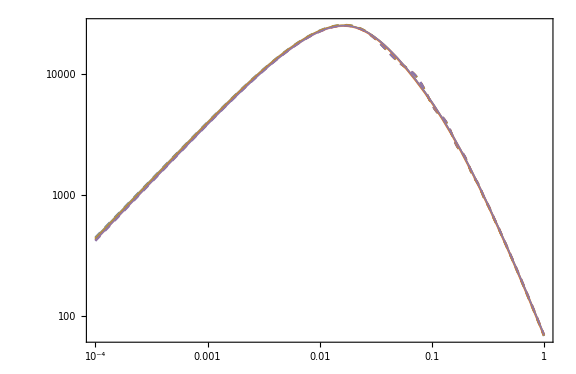

```mathematica
(* Graphic comparison *)
ListLogLogPlot[{Pkns[[1]],Pkns[[2]],Pkns[[3]],Pkns[[4]],Pkns[[5]]},Joined->True,PlotRange->All,PlotStyle->{Dashed},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["n_s = 0.96"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["n_s = 0.9625"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["n_s = 0.965"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["n_s = 0.9675"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["n_s = 0.97"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.52,0.25}],AspectRatio->0.65,ImageSize->720];//Quiet
LogLogPlot[{P[k,w,k0,β,s]/.Parns0.b496[[2]],P[k,w,k0,β,s]/.Parns0.b49625[[2]],P[k,w,k0,β,s]/.Parns0.b4965[[2]],P[k,w,k0,β,s]/.Parns0.b49675[[2]],P[k,w,k0,β,s]/.Parns0.b497[[2]]}//Evaluate,{k,Pkns[[5]][[1,1]],Pkns[[5]][[-1,1]]},PlotRange->All,PlotStyle->{Thick,Opacity[0.6]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];//Quiet
Show[{%%,%},PlotRange->All,ImageSize->Large]//Quiet
```

# Matter Power Spectrum: α_B

## propto_scale

## Data

```mathematica
(* Import datasets *)
Braiding.b4Files="/Users/cosmology/hi_class_public/output/propto_scale/Braiding/";
PkB0=Import[Braiding.b4Files<>"B_0_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b41=Import[Braiding.b4Files<>"B_0.1_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b42=Import[Braiding.b4Files<>"B_0.2_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b43=Import[Braiding.b4Files<>"B_0.3_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b44=Import[Braiding.b4Files<>"B_0.4_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b45=Import[Braiding.b4Files<>"B_0.5_pk.dat","Data"][[5;;-1]]//Quiet;
PkB0.b46=Import[Braiding.b4Files<>"B_0.6_pk.dat","Data"][[5;;-1]]//Quiet;
```

```mathematica
(* Power spectrum for wCDM from GA *)
Pw[k_,w_]:=(2.5239506940685576*^6 k^0.9645201679721765 (1+0.7106356245167889 w^3+1.8801896647991612 w^4+0.939216799027307 w^5))/(√(1+1395.2489187744666 k^1.4917653903428132+2.3729066856033597*^7 k^4.027553399922359+1.1994340119292421*^9 k^6.0600043498512886+7.611601220332279*^8 k^7.284778673036612))
```

```mathematica
ns=0.9619;
S[s_]:=3*10^6*(1+s) (* Shift factor *)
Psup[k_,s_]:=S[s]*k^ns; (* Primordial spectrum *)
Psub[k_,w_]:=Pw[k,w] (* wCDM P(k,w) *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(k-k0)/β)); (* Transition function *)
P[k_,w_,k0_,β_,s_]:=(1-σ[k,k0,β])Psup[k,s]+σ[k,k0,β]*Psub[k,w] (* Total spectrum *)
```

## Comparison

```mathematica
(* Accuracy for each dataset *)
χ2αB0.b41[w_,k0_,β_,s_]:=Mean[Table[Abs[PkB0.b41⟦i,2⟧-P[PkB0.b41⟦i,1⟧,w,k0,β,s]]/(PkB0.b41⟦i,2⟧)*100,{i,1,Length[PkB0.b41]}]]
χ2αB0.b42[w_,k0_,β_,s_]:=Mean[Table[Abs[PkB0.b42⟦i,2⟧-P[PkB0.b42⟦i,1⟧,w,k0,β,s]]/(PkB0.b42⟦i,2⟧)*100,{i,1,Length[PkB0.b42]}]]
χ2αB0.b43[w_,k0_,β_,s_]:=Mean[Table[Abs[PkB0.b43⟦i,2⟧-P[PkB0.b43⟦i,1⟧,w,k0,β,s]]/(PkB0.b43⟦i,2⟧)*100,{i,1,Length[PkB0.b43]}]]
χ2αB0.b44[w_,k0_,β_,s_]:=Mean[Table[Abs[PkB0.b44⟦i,2⟧-P[PkB0.b44⟦i,1⟧,w,k0,β,s]]/(PkB0.b44⟦i,2⟧)*100,{i,1,Length[PkB0.b44]}]]
χ2αB0.b45[w_,k0_,β_,s_]:=Mean[Table[Abs[PkB0.b45⟦i,2⟧-P[PkB0.b45⟦i,1⟧,w,k0,β,s]]/(PkB0.b45⟦i,2⟧)*100,{i,1,Length[PkB0.b45]}]]
χ2αB0.b46[w_,k0_,β_,s_]:=Mean[Table[Abs[PkB0.b46⟦i,2⟧-P[PkB0.b46⟦i,1⟧,w,k0,β,s]]/(PkB0.b46⟦i,2⟧)*100,{i,1,Length[PkB0.b46]}]]
```

```mathematica
(* Compute the most accurate set of parameters *)
ParαB0.b41=FindMinimum[χ2αB0.b41[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0006},{β,0.0001,0.0007},{s,-0.22,-0.4}}]
ParαB0.b42=FindMinimum[χ2αB0.b42[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0006},{β,0.0001,0.0007},{s,-0.22,-0.4}}]
ParαB0.b43=FindMinimum[χ2αB0.b43[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0006},{β,0.0001,0.0007},{s,-0.22,-0.4}}]
ParαB0.b44=FindMinimum[χ2αB0.b44[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0006},{β,0.0001,0.0007},{s,-0.22,-0.4}}]
ParαB0.b45=FindMinimum[χ2αB0.b45[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0006},{β,0.0001,0.0007},{s,-0.22,-0.4}}]
ParαB0.b46=FindMinimum[χ2αB0.b46[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0006},{β,0.0001,0.0007},{s,-0.22,-0.4}}]
```

{1.65593,{w→0.566662,k0→0.0000134002,β→0.00219893,s→-0.0014075}}

{1.59406,{w→0.597287,k0→0.0000494517,β→0.00198989,s→-0.151385}}

{1.71599,{w→0.62603,k0→0.000157041,β→0.00138271,s→-0.333506}}

{1.70386,{w→0.653793,k0→0.00106856,β→0.000669062,s→-0.232791}}

{1.73132,{w→0.681424,k0→0.00113446,β→0.00042595,s→-0.2712}}

{1.96648,{w→0.71247,k0→0.00109012,β→0.000419673,s→-0.396997}}

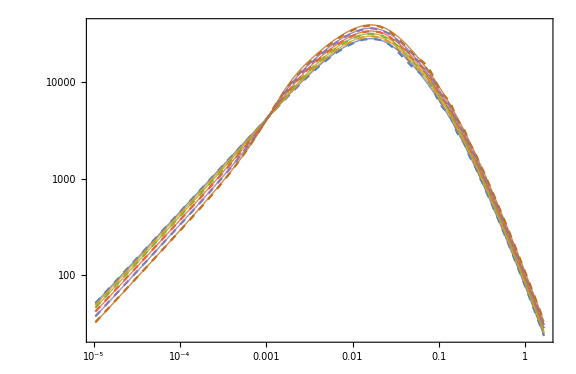

```mathematica
(* Graphic comparison *)
ListLogLogPlot[{PkB0.b41,PkB0.b42,PkB0.b43,PkB0.b44,PkB0.b45,PkB0.b46},Joined->True,PlotRange->All,PlotStyle->{Dashed},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.1"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.2"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.3"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.4"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.5"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.6"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.6,0.3}],ImageSize->720];
LogLogPlot[{P[k,w,k0,β,s]/.ParαB0.b41[[2]],P[k,w,k0,β,s]/.ParαB0.b42[[2]],P[k,w,k0,β,s]/.ParαB0.b43[[2]],P[k,w,k0,β,s]/.ParαB0.b44[[2]],P[k,w,k0,β,s]/.ParαB0.b45[[2]],P[k,w,k0,β,s]/.ParαB0.b46[[2]]}//Evaluate,{k,PkB0[[1,1]],PkB0[[-1,1]]},PlotRange->All,PlotStyle->{Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick],Directive[Opacity[0.8],Thick]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];
Show[{%%,%},PlotRange->All,ImageSize->Large]
```

## propto_omega

## Data

```mathematica
(* Import datasets *)
Braiding.b4Files="/Users/cosmology/hi_class_public/output/propto_omega/Braiding/";
PkB0.b4625=Import[Braiding.b4Files<>"B_0.625_pk.dat","Data"][[5;;-1]]//Quiet;
PkB1.b425=Import[Braiding.b4Files<>"B_1.25_pk.dat","Data"][[5;;-1]]//Quiet;
PkB1.b4875=Import[Braiding.b4Files<>"B_1.875_pk.dat","Data"][[5;;-1]]//Quiet;
PkB2.b45=Import[Braiding.b4Files<>"B_2.5_pk.dat","Data"][[5;;-1]]//Quiet;
```

```mathematica
(* Power spectrum for wCDM from GA *)
Pw[k_,w_]:=(2.5239506940685576*^6 k^0.9645201679721765 (1+0.7106356245167889 w^3+1.8801896647991612 w^4+0.939216799027307 w^5))/(√(1+1395.2489187744666 k^1.4917653903428132+2.3729066856033597*^7 k^4.027553399922359+1.1994340119292421*^9 k^6.0600043498512886+7.611601220332279*^8 k^7.284778673036612))
```

```mathematica
ns=0.9619;
S[s_]:=3*10^6*(1+s) (* Shift factor *)
Psup[k_,s_]:=S[s]*k^ns; (* Primordial spectrum *)
Psub[k_,w_]:=Pw[k,w] (* wCDM P(k,w) *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(k-k0)/β)); (* Transition function *)
P[k_,w_,k0_,β_,s_]:=(1-σ[k,k0,β])Psup[k,s]+σ[k,k0,β]*Psub[k,w] (* Total spectrum *)
```

## Comparison

```mathematica
(* Accuracy for each dataset *)
χ2αB0.b4625[w_,k0_,β_,s_]:=Mean[Table[Abs[PkB0.b4625⟦i,2⟧-P[PkB0.b4625⟦i,1⟧,w,k0,β,s]]/(PkB0.b4625⟦i,2⟧)*100,{i,1,Length[PkB0.b4625]}]]
χ2P1.b425[w_,k0_,β_,s_]:=Mean[Table[Abs[PkB1.b425⟦i,2⟧-P[PkB1.b425⟦i,1⟧,w,k0,β,s]]/(PkB1.b425⟦i,2⟧)*100,{i,1,Length[PkB1.b425]}]]
χ2P1.b4875[w_,k0_,β_,s_]:=Mean[Table[Abs[PkB1.b4875⟦i,2⟧-P[PkB1.b4875⟦i,1⟧,w,k0,β,s]]/(PkB1.b4875⟦i,2⟧)*100,{i,1,Length[PkB1.b4875]}]]
χ2P2.b45[w_,k0_,β_,s_]:=Mean[Table[Abs[PkB2.b45⟦i,2⟧-P[PkB2.b45⟦i,1⟧,w,k0,β,s]]/(PkB2.b45⟦i,2⟧)*100,{i,1,Length[PkB2.b45]}]]
```

```mathematica
(* Compute the most accurate set of parameters *)
ParαB0.b4625=FindMinimum[χ2αB0.b4625[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.001},{β,0.0001,0.001},{s,-0.2,-0.4}}]
Par1.b425=FindMinimum[χ2P1.b425[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.001},{β,0.0001,0.001},{s,-0.2,-0.4}}]
Par1.b4875=FindMinimum[χ2P1.b4875[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.001},{β,0.0001,0.001},{s,-1,0}}]
Par2.b45=FindMinimum[χ2P2.b45[w,k0,β,s],{{w,0,2},{k0,0.00001,0.001},{β,0.0001,0.001},{s,-1,0}}]
```

{1.58229,{w→0.550522,k0→0.0000951094,β→0.000672659,s→-0.240643}}

{1.69114,{w→0.566876,k0→0.000624595,β→0.000398961,s→-0.354187}}

{1.91816,{w→0.585068,k0→0.000028636,β→0.000730848,s→-0.932219}}

{2.04835,{w→0.605222,k0→0.0000789156,β→0.000793923,s→-1.08699}}

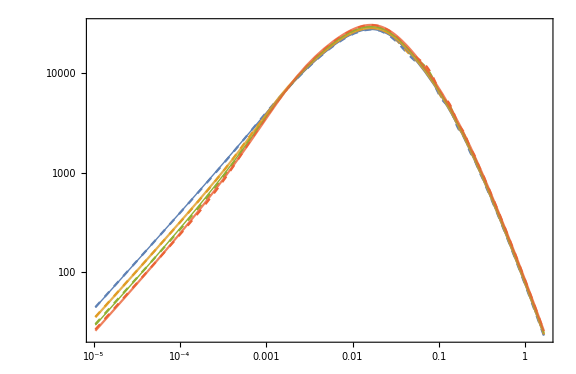

```mathematica
(* Graphic comparison *)
ListLogLogPlot[{PkB0.b4625,PkB1.b425,PkB1.b4875,PkB2.b45},Joined->True,PlotRange->All,PlotStyle->{Dashed},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.625"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 1.25"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 1.875"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 2.5"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.6,0.3}],ImageSize->720];
LogLogPlot[{P[k,w,k0,β,s]/.ParαB0.b4625[[2]],P[k,w,k0,β,s]/.Par1.b425[[2]],P[k,w,k0,β,s]/.Par1.b4875[[2]],P[k,w,k0,β,s]/.Par2.b45[[2]]}//Evaluate,{k,PkB0[[1,1]],PkB0[[-1,1]]},PlotRange->All,PlotStyle->{Thick,Opacity[0.8]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];
Show[{%%,%},PlotRange->All,ImageSize->Large]
```

# Matter Power Spectrum: α_M

## propto_scale

## Data

```mathematica
(* Import datasets *)
Running.b4Files="/Users/cosmology/hi_class_public/output/propto_scale/Running/";
PkM0=Import[Running.b4Files<>"M_0_pk.dat","Data"][[5;;-1]]//Quiet;
PkM0.b425=Import[Running.b4Files<>"M_0.25_pk.dat","Data"][[5;;-1]]//Quiet;
PkM0.b45=Import[Running.b4Files<>"M_0.5_pk.dat","Data"][[5;;-1]]//Quiet;
PkM0.b475=Import[Running.b4Files<>"M_0.75_pk.dat","Data"][[5;;-1]]//Quiet;
PkM1=Import[Running.b4Files<>"M_1_pk.dat","Data"][[5;;-1]]//Quiet;
```

```mathematica
(* Power spectrum for wCDM from GA *)
Pw[k_,w_]:=(2.5239506940685576*^6 k^0.9645201679721765 (1+0.7106356245167889 w^3+1.8801896647991612 w^4+0.939216799027307 w^5))/(√(1+1395.2489187744666 k^1.4917653903428132+2.3729066856033597*^7 k^4.027553399922359+1.1994340119292421*^9 k^6.0600043498512886+7.611601220332279*^8 k^7.284778673036612))
ns=0.9619;
S[s_]:=3*10^6*(1+s) (* Shift factor *)
Psup[k_,s_]:=S[s]*k^ns; (* Primordial spectrum *)
Psub[k_,w_]:=Pw[k,w] (* wCDM P(k,w) *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(k-k0)/β)); (* Transition function *)
P[k_,w_,k0_,β_,s_]:=(1-σ[k,k0,β])Psup[k,s]+σ[k,k0,β]*Psub[k,w] (* Total spectrum *)
```

## Comparison

```mathematica
(* Accuracy for each dataset *)
χ2P0.b425[w_,k0_,β_,s_]:=Mean[Table[Abs[PkM0.b425⟦i,2⟧-P[PkM0.b425⟦i,1⟧,w,k0,β,s]]/(PkM0.b425⟦i,2⟧)*100,{i,1,Length[PkM0.b425]}]]
χ2αM0.b45[w_,k0_,β_,s_]:=Mean[Table[Abs[PkM0.b45⟦i,2⟧-P[PkM0.b45⟦i,1⟧,w,k0,β,s]]/(PkM0.b45⟦i,2⟧)*100,{i,1,Length[PkM0.b45]}]]
χ2P0.b475[w_,k0_,β_,s_]:=Mean[Table[Abs[PkM0.b475⟦i,2⟧-P[PkM0.b475⟦i,1⟧,w,k0,β,s]]/(PkM0.b475⟦i,2⟧)*100,{i,1,Length[PkM0.b475]}]]
χ2P1[w_,k0_,β_,s_]:=Mean[Table[Abs[PkM1⟦i,2⟧-P[PkM1⟦i,1⟧,w,k0,β,s]]/PkM1⟦i,2⟧*100,{i,1,Length[PkM1]}]]
```

```mathematica
(* Compute the most accurate set of parameters *)
Par0.b425=FindMinimum[χ2P0.b425[w,k0,β,s],{{w,0,1},{k0,0.00001,0.001},{β,0.0001,0.001},{s,1,2}}]
ParαM0.b45=FindMinimum[χ2αM0.b45[w,k0,β,s],{{w,0,1},{k0,0.0001,0.001},{β,0.0001,0.001},{s,1,4}}]
Par0.b475=FindMinimum[χ2P0.b475[w,k0,β,s],{{w,-1.3,0},{k0,0.0001,0.01},{β,0.001,0.01},{s,2,3}}]
Par1=FindMinimum[χ2P1[w,k0,β,s],{{w,-1.3,0},{k0,0.0001,0.01},{β,0.0001,0.01},{s,2,3}}]
```

{1.58053,{w→0.468838,k0→-0.0000756543,β→0.000943025,s→0.482221}}

{1.79739,{w→0.372509,k0→0.0000873899,β→0.000661962,s→1.15611}}

{2.03774,{w→-1.50056,k0→0.000132706,β→0.000525521,s→2.00077}}

{2.31528,{w→-1.52475,k0→0.000295691,β→0.000391838,s→2.53904}}

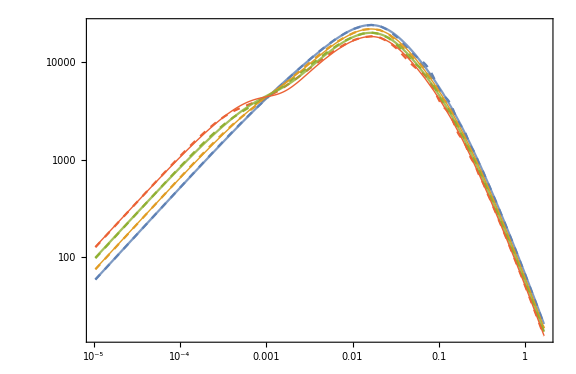

```mathematica
(* Graphic comparison *)
ListLogLogPlot[{PkM0.b425,PkM0.b45,PkM0.b475,PkM1},Joined->True,PlotRange->All,PlotStyle->{Dashed},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.25"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.5"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.75"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 1"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.55,0.3}],AspectRatio->0.65,ImageSize->720];
LogLogPlot[{P[k,w,k0,β,s]/.Par0.b425[[2]],P[k,w,k0,β,s]/.ParαM0.b45[[2]],P[k,w,k0,β,s]/.Par0.b475[[2]],P[k,w,k0,β,s]/.Par1[[2]]}//Evaluate,{k,PkM0[[1,1]],PkM0[[-1,1]]},PlotRange->All,PlotStyle->{Opacity[0.8],Thick},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];
Show[{%%,%},PlotRange->All,ImageSize->Large]
```

## propto_omega

## Data

```mathematica
(* Import datasets *)
Running.b4Files="/Users/cosmology/hi_class_public/output/propto_omega/Running/";
PkM0=Import[Running.b4Files<>"M_0_pk.dat","Data"][[5;;-1]]//Quiet;
PkM1=Import[Running.b4Files<>"M_1_pk.dat","Data"][[5;;-1]]//Quiet;
PkM2=Import[Running.b4Files<>"M_2_pk.dat","Data"][[5;;-1]]//Quiet;
PkM3=Import[Running.b4Files<>"M_3_pk.dat","Data"][[5;;-1]]//Quiet;
PkM4=Import[Running.b4Files<>"M_4_pk.dat","Data"][[5;;-1]]//Quiet;
```

```mathematica
(* Power spectrum for wCDM from GA *)
Pw[k_,w_]:=(2.5239506940685576*^6 k^0.9645201679721765 (1+0.7106356245167889 w^3+1.8801896647991612 w^4+0.939216799027307 w^5))/(√(1+1395.2489187744666 k^1.4917653903428132+2.3729066856033597*^7 k^4.027553399922359+1.1994340119292421*^9 k^6.0600043498512886+7.611601220332279*^8 k^7.284778673036612))
ns=0.9619;
S[s_]:=3*10^6*(1+s) (* Shift factor *)
Psup[k_,s_]:=S[s]*k^ns; (* Primordial spectrum *)
Psub[k_,w_]:=Pw[k,w] (* wCDM P(k,w) *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(k-k0)/β)); (* Transition function *)
P[k_,w_,k0_,β_,s_]:=(1-σ[k,k0,β])Psup[k,s]+σ[k,k0,β]*Psub[k,w] (* Total spectrum *)
```

## Comparison

```mathematica
(* Accuracy for each dataset *)
χ2P1[w_,k0_,β_,s_]:=Mean[Table[Abs[PkM1⟦i,2⟧-P[PkM1⟦i,1⟧,w,k0,β,s]]/PkM1⟦i,2⟧*100,{i,1,Length[PkM1]}]]
χ2P2[w_,k0_,β_,s_]:=Mean[Table[Abs[PkM2⟦i,2⟧-P[PkM2⟦i,1⟧,w,k0,β,s]]/PkM2⟦i,2⟧*100,{i,1,Length[PkM2]}]]
χ2αMP3[w_,k0_,β_,s_]:=Mean[Table[Abs[PkM3⟦i,2⟧-P[PkM3⟦i,1⟧,w,k0,β,s]]/PkM3⟦i,2⟧*100,{i,1,Length[PkM3]}]]
χ2P4[w_,k0_,β_,s_]:=Mean[Table[Abs[PkM4⟦i,2⟧-P[PkM4⟦i,1⟧,w,k0,β,s]]/PkM4⟦i,2⟧*100,{i,1,Length[PkM4]}]]
```

```mathematica
(* Compute the most accurate set of parameters *)
Par1=FindMinimum[χ2P1[w,k0,β,s],{{w,0.2,1},{k0,0.0001,0.001},{β,0.0001,0.001},{s,1,2}}]
Par2=FindMinimum[χ2P2[w,k0,β,s],{{w,0.2,1},{k0,0.0001,0.001},{β,0.0001,0.001},{s,1,2}}]
ParαM3=FindMinimum[χ2αMP3[w,k0,β,s],{{w,0.2,1},{k0,0.0001,0.001},{β,0.0001,0.001},{s,1,2}}]
Par4=FindMinimum[χ2P4[w,k0,β,s],{{w,0.2,1},{k0,0.0001,0.001},{β,0.0001,0.001},{s,2,3}}]
```

{1.52613,{w→0.561728,k0→-0.0000303918,β→0.000660207,s→0.452091}}

{1.66775,{w→0.579561,k0→0.000317137,β→0.000331124,s→1.09237}}

{1.82927,{w→0.591395,k0→0.000291262,β→0.000246395,s→2.07024}}

{1.97841,{w→0.59889,k0→0.000197591,β→0.000242942,s→3.75513}}

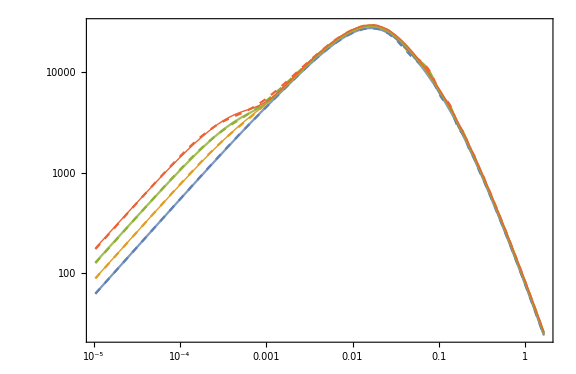

```mathematica
(* Graphic comparison *)
ListLogLogPlot[{PkM1,PkM2,PkM3,PkM4},Joined->True,PlotRange->All,PlotStyle->{Dashed},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 1"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 2"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 3"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 4"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.55,0.3}],AspectRatio->0.65,ImageSize->720];
LogLogPlot[{P[k,w,k0,β,s]/.Par1[[2]],P[k,w,k0,β,s]/.Par2[[2]],P[k,w,k0,β,s]/.ParαM3[[2]],P[k,w,k0,β,s]/.Par4[[2]]}//Evaluate,{k,PkM0[[1,1]],PkM0[[-1,1]]},PlotRange->All,PlotStyle->{Opacity[0.8],Thick},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];
Show[{%%,%},PlotRange->All,ImageSize->Large]
```

# Matter Power Spectrum: α_T

## propto_scale

## Data

```mathematica
(* Import datasets *)
Excess.b4Files="/Users/cosmology/hi_class_public/output/propto_scale/Excess/";
PkT0=Import[Excess.b4Files<>"T_0_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b425=Import[Excess.b4Files<>"T_0.25_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b45=Import[Excess.b4Files<>"T_0.5_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b475=Import[Excess.b4Files<>"T_0.75_pk.dat","Data"][[5;;-1]]//Quiet;
PkT1=Import[Excess.b4Files<>"T_1_pk.dat","Data"][[5;;-1]]//Quiet;
```

```mathematica
(* Power spectrum for wCDM from GA *)
Pw[k_,w_]:=(2.5239506940685576*^6 k^0.9645201679721765 (1+0.7106356245167889 w^3+1.8801896647991612 w^4+0.939216799027307 w^5))/(√(1+1395.2489187744666 k^1.4917653903428132+2.3729066856033597*^7 k^4.027553399922359+1.1994340119292421*^9 k^6.0600043498512886+7.611601220332279*^8 k^7.284778673036612))
ns=0.9619;
S[s_]:=3*10^6*(1+s) (* Shift factor *)
Psup[k_,s_]:=S[s]*k^ns; (* Primordial spectrum *)
Psub[k_,w_]:=Pw[k,w] (* wCDM P(k,w) *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(k-k0)/β)); (* Transition function *)
P[k_,w_,k0_,β_,s_]:=(1-σ[k,k0,β])Psup[k,s]+σ[k,k0,β]*Psub[k,w] (* Total spectrum *)
```

## Comparison

```mathematica
(* Accuracy for each dataset *)
χ2P0[w_,k0_,β_,s_]:=Mean[Table[Abs[PkT0⟦i,2⟧-P[PkT0⟦i,1⟧,w,k0,β,s]]/PkT0⟦i,2⟧*100,{i,1,Length[PkT0]}]]
χ2P0.b425[w_,k0_,β_,s_]:=Mean[Table[Abs[PkT0.b425⟦i,2⟧-P[PkT0.b425⟦i,1⟧,w,k0,β,s]]/(PkT0.b425⟦i,2⟧)*100,{i,1,Length[PkT0.b425]}]]
χ2αT0.b45[w_,k0_,β_,s_]:=Mean[Table[Abs[PkT0.b45⟦i,2⟧-P[PkT0.b45⟦i,1⟧,w,k0,β,s]]/(PkT0.b45⟦i,2⟧)*100,{i,1,Length[PkT0.b45]}]]
χ2P0.b475[w_,k0_,β_,s_]:=Mean[Table[Abs[PkT0.b475⟦i,2⟧-P[PkT0.b475⟦i,1⟧,w,k0,β,s]]/(PkT0.b475⟦i,2⟧)*100,{i,1,Length[PkT0.b475]}]]
χ2αT1[w_,k0_,β_,s_]:=Mean[Table[Abs[PkT1⟦i,2⟧-P[PkT1⟦i,1⟧,w,k0,β,s]]/PkT1⟦i,2⟧*100,{i,1,Length[PkT1]}]]
```

```mathematica
(* Compute the most accurate set of parameters *)
Par0=FindMinimum[χ2P0[w,k0,β,s],{w,k0,β,s}]//Quiet
Par0.b425=FindMinimum[χ2P0.b425[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0004},{β,0.0002,0.0007},{s,-0.22,-0.25}}]
ParαT0.b45=FindMinimum[χ2αT0.b45[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0006},{β,0.0001,0.0007},{s,-0.22,-0.4}}]
Par0.b475=FindMinimum[χ2P0.b475[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0005},{β,0.0001,0.0007},{s,-0.22,-0.5}}]
ParαT1=FindMinimum[χ2αT1[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0005},{β,0.0002,0.0007},{s,-0.2,-0.6}}]
```

{1.6288,{w→0.535965,k0→-0.359257,β→0.0254363,s→-0.226659}}

{1.4964,{w→0.534777,k0→0.000767174,β→0.000320816,s→-0.0906207}}

{1.55487,{w→0.53385,k0→0.000545341,β→0.000202222,s→-0.24193}}

{1.61194,{w→0.533639,k0→0.000441799,β→0.000173956,s→-0.390388}}

{1.72162,{w→0.53566,k0→0.000395187,β→0.000140277,s→-0.508838}}

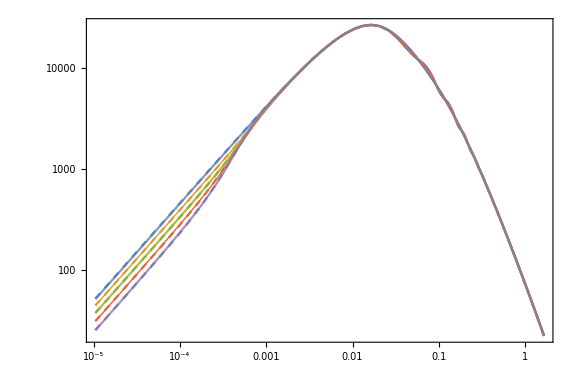

```mathematica
(* Graphic comparison *)
ListLogLogPlot[{PkT0,PkT0.b425,PkT0.b45,PkT0.b475,PkT1},Joined->True,PlotRange->All,PlotStyle->{Dashed},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = 0"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.25"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.5"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.75"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -1"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.55,0.3}],ImageSize->720];
LogLogPlot[{P[k,w,k0,β,s]/.Par0[[2]],P[k,w,k0,β,s]/.Par0.b425[[2]],P[k,w,k0,β,s]/.ParαT0.b45[[2]],P[k,w,k0,β,s]/.Par0.b475[[2]],P[k,w,k0,β,s]/.ParαT1[[2]]}//Evaluate,{k,PkT0.b425[[1,1]],PkT0.b425[[-1,1]]},PlotRange->All,PlotStyle->{Opacity[0.8],Thick},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];
Show[{%%,%},PlotRange->All,ImageSize->Large]
```

## propto_omega

## Data

```mathematica
(* Import datasets *)
Excess.b4Files="/Users/cosmology/hi_class_public/output/propto_omega/Excess/";
PkT0=Import[Excess.b4Files<>"T_0_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b425=Import[Excess.b4Files<>"T_0.25_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b45=Import[Excess.b4Files<>"T_0.5_pk.dat","Data"][[5;;-1]]//Quiet;
PkT0.b475=Import[Excess.b4Files<>"T_0.75_pk.dat","Data"][[5;;-1]]//Quiet;
PkT1=Import[Excess.b4Files<>"T_1_pk.dat","Data"][[5;;-1]]//Quiet;
PkT1.b425=Import[Excess.b4Files<>"T_1.25_pk.dat","Data"][[5;;-1]]//Quiet;
```

```mathematica
(* Power spectrum for wCDM from GA *)
Pw[k_,w_]:=(2.5239506940685576*^6 k^0.9645201679721765 (1+0.7106356245167889 w^3+1.8801896647991612 w^4+0.939216799027307 w^5))/(√(1+1395.2489187744666 k^1.4917653903428132+2.3729066856033597*^7 k^4.027553399922359+1.1994340119292421*^9 k^6.0600043498512886+7.611601220332279*^8 k^7.284778673036612))
ns=0.9619;
S[s_]:=3*10^6*(1+s) (* Shift factor *)
Psup[k_,s_]:=S[s]*k^ns; (* Primordial spectrum *)
Psub[k_,w_]:=Pw[k,w] (* wCDM P(k,w) *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(k-k0)/β)); (* Transition function *)
P[k_,w_,k0_,β_,s_]:=(1-σ[k,k0,β])Psup[k,s]+σ[k,k0,β]*Psub[k,w] (* Total spectrum *)
```

## Comparison

```mathematica
(* Accuracy for each dataset *)
χ2P0[w_,k0_,β_,s_]:=Mean[Table[Abs[PkT0⟦i,2⟧-P[PkT0⟦i,1⟧,w,k0,β,s]]/PkT0⟦i,2⟧*100,{i,1,Length[PkT0]}]]
χ2αT0.b425[w_,k0_,β_,s_]:=Mean[Table[Abs[PkT0.b425⟦i,2⟧-P[PkT0.b425⟦i,1⟧,w,k0,β,s]]/(PkT0.b425⟦i,2⟧)*100,{i,1,Length[PkT0.b425]}]]
χ2P0.b45[w_,k0_,β_,s_]:=Mean[Table[Abs[PkT0.b45⟦i,2⟧-P[PkT0.b45⟦i,1⟧,w,k0,β,s]]/(PkT0.b45⟦i,2⟧)*100,{i,1,Length[PkT0.b45]}]]
χ2P0.b475[w_,k0_,β_,s_]:=Mean[Table[Abs[PkT0.b475⟦i,2⟧-P[PkT0.b475⟦i,1⟧,w,k0,β,s]]/(PkT0.b475⟦i,2⟧)*100,{i,1,Length[PkT0.b475]}]]
χ2αTΩ1[w_,k0_,β_,s_]:=Mean[Table[Abs[PkT1⟦i,2⟧-P[PkT1⟦i,1⟧,w,k0,β,s]]/PkT1⟦i,2⟧*100,{i,1,Length[PkT1]}]]
χ2P1.b425[w_,k0_,β_,s_]:=Mean[Table[Abs[PkT1.b425⟦i,2⟧-P[PkT1.b425⟦i,1⟧,w,k0,β,s]]/(PkT1.b425⟦i,2⟧)*100,{i,1,Length[PkT1.b425]}]]
```

```mathematica
(* Compute the most accurate set of parameters *)
Par0=FindMinimum[χ2P0[w,k0,β,s],{w,k0,β,s}]//Quiet
ParαT0.b425=FindMinimum[χ2P0.b425[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0004},{β,0.0002,0.0007},{s,-0.22,-0.25}}]
Par0.b45=FindMinimum[χ2P0.b45[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0006},{β,0.0001,0.0007},{s,-0.22,-0.4}}]
Par0.b475=FindMinimum[χ2P0.b475[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0005},{β,0.0001,0.0007},{s,-0.22,-0.5}}]
ParαTΩ1=FindMinimum[χ2αTΩ1[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0005},{β,0.0002,0.0007},{s,-0.2,-0.6}}]
Par1.b425=FindMinimum[χ2P1.b425[w,k0,β,s],{{w,0,1.4},{k0,0.0001,0.0005},{β,0.0002,0.0007},{s,-0.2,-0.6}}]
```

{1.62891,{w→0.535965,k0→-0.359256,β→0.0254364,s→-0.226659}}

{1.49856,{w→0.534916,k0→-0.00020422,β→0.00109803,s→-0.0360739}}

{1.54552,{w→0.534946,k0→-1.81025×10^-6,β→0.000593252,s→-0.144907}}

{1.58537,{w→0.534936,k0→0.000071354,β→0.000464031,s→-0.236867}}

{1.53933,{w→0.534247,k0→0.000369,β→0.000267792,s→-0.202059}}

{1.55512,{w→0.534216,k0→0.00041444,β→0.000134839,s→-0.206739}}

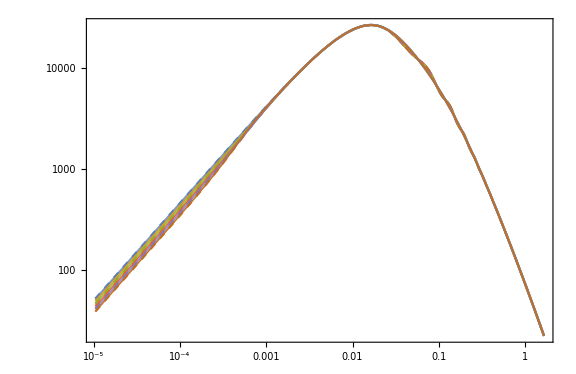

```mathematica
(* Graphic comparison *)
ListLogLogPlot[{PkT0,PkT0.b425,PkT0.b45,PkT0.b475,PkT1,PkT1.b425},Joined->True,PlotRange->All,PlotStyle->{Dashed},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = 0"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.25"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.5"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -0.75"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -1"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_T = -1.25"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.57,0.3}],ImageSize->720];
LogLogPlot[{P[k,w,k0,β,s]/.Par0[[2]],P[k,w,k0,β,s]/.ParαT0.b425[[2]],P[k,w,k0,β,s]/.Par0.b45[[2]],P[k,w,k0,β,s]/.Par0.b475[[2]],P[k,w,k0,β,s]/.ParαTΩ1[[2]],P[k,w,k0,β,s]/.Par1.b425[[2]]}//Evaluate,{k,PkT0.b425[[1,1]],PkT0.b425[[-1,1]]},PlotRange->All,PlotStyle->{Opacity[0.8],Thick},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];
Show[{%%,%},PlotRange->All,ImageSize->Large]
```

# Matter Power Spectrum: plk_late

## Data

```mathematica
(* Import datasets *)
plk.b4Files="/Users/cosmology/mgclass--ii/output/plk_late/";
PkE110.b4E220=Import[plk.b4Files<>"E11_0_E22_0_pk.dat","Data"][[7;;-1]]//Quiet;
PkE111.b4E221=Import[plk.b4Files<>"E11_1_E22_1_pk.dat","Data"][[7;;-1]]//Quiet;
PkE111n.b4E221n=Import[plk.b4Files<>"E11_1n_E22_1n_pk.dat","Data"][[7;;-1]]//Quiet;
PkE1105.b4E2205=Import[plk.b4Files<>"E11_0.5_E22_0.5_pk.dat","Data"][[7;;-1]]//Quiet;
PkE1105n.b4E2205n=Import[plk.b4Files<>"E11_0.5n_E22_0.5n_pk.dat","Data"][[7;;-1]]//Quiet;
PkE110.b4E221=Import[plk.b4Files<>"E11_0_E22_1_pk.dat","Data"][[7;;-1]]//Quiet;
```

```mathematica
(* Power spectrum for wCDM from GA *)
Pw[k_,w_]:=(2.5239506940685576*^6 k^0.9645201679721765 (1+0.7106356245167889 w^3+1.8801896647991612 w^4+0.939216799027307 w^5))/(√(1+1395.2489187744666 k^1.4917653903428132+2.3729066856033597*^7 k^4.027553399922359+1.1994340119292421*^9 k^6.0600043498512886+7.611601220332279*^8 k^7.284778673036612))
ns=0.9619;
S[s_]:=3*10^6*(1+s) (* Shift factor *)
Psup[k_,s_]:=S[s]*k^ns; (* Primordial spectrum *)
Psub[k_,w_]:=Pw[k,w] (* wCDM P(k,w) *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(k-k0)/β)); (* Transition function *)
P[k_,w_,k0_,β_,s_]:=(1-σ[k,k0,β])Psup[k,s]+σ[k,k0,β]*Psub[k,w] (* Total spectrum *)
```

## Comparison

```mathematica
(* Accuracy for each dataset *)
χ2E111.b4E221[w_,k0_,β_,s_]:=Mean[Table[Abs[PkE111.b4E221⟦i,2⟧-P[PkE111.b4E221⟦i,1⟧,w,k0,β,s]]/(PkE111.b4E221⟦i,2⟧)*100,{i,1,Length[PkE111.b4E221]}]]
χ2E111n.b4E221n[w_,k0_,β_,s_]:=Mean[Table[Abs[PkE111n.b4E221n⟦i,2⟧-P[PkE111n.b4E221n⟦i,1⟧,w,k0,β,s]]/(PkE111n.b4E221n⟦i,2⟧)*100,{i,1,Length[PkE111n.b4E221n]}]]
χ2E1105.b4E2205[w_,k0_,β_,s_]:=Mean[Table[Abs[PkE1105.b4E2205⟦i,2⟧-P[PkE1105.b4E2205⟦i,1⟧,w,k0,β,s]]/(PkE1105.b4E2205⟦i,2⟧)*100,{i,1,Length[PkE1105.b4E2205]}]]
χ2E1105n.b4E2205n[w_,k0_,β_,s_]:=Mean[Table[Abs[PkE1105n.b4E2205n⟦i,2⟧-P[PkE1105n.b4E2205n⟦i,1⟧,w,k0,β,s]]/(PkE1105n.b4E2205n⟦i,2⟧)*100,{i,1,Length[PkE1105n.b4E2205n]}]]
χ2E110.b4E221[w_,k0_,β_,s_]:=Mean[Table[Abs[PkE110.b4E221⟦i,2⟧-P[PkE110.b4E221⟦i,1⟧,w,k0,β,s]]/(PkE110.b4E221⟦i,2⟧)*100,{i,1,Length[PkE110.b4E221]}]]
```

```mathematica
(* Compute the most accurate set of parameters *)
ParE111.b4E221=FindMinimum[χ2E111.b4E221[w,k0,β,s],{{w,0.5,0.61},{k0,0.0001,0.001},{β,0.0001,0.001},{s,-1,0}}]
ParE111n.b4E221n=FindMinimum[χ2E111n.b4E221n[w,k0,β,s],{{w,0.1,0.5},{k0,0.0001,0.01},{β,0.001,0.1},{s,10,11}}]
ParE1105.b4E2205=FindMinimum[χ2E1105.b4E2205[w,k0,β,s],{{w,0.1,1},{k0,0.00001,0.001},{β,0.0001,0.01},{s,-1,0}}]
ParE1105n.b4E2205n=FindMinimum[χ2E1105n.b4E2205n[w,k0,β,s],{{w,0.2,0.5},{k0,0.00001,0.001},{β,0.0001,0.01},{s,0,50}}]
ParE110.b4E221=FindMinimum[χ2E110.b4E221[w,k0,β,s],{{w,0.8,1},{k0,0.0001,0.001},{β,0.0001,0.001},{s,-1,0}}]
```

{2.08486,{w→0.588176,k0→0.000821564,β→0.000607609,s→-1.13625}}

{3.15749,{w→0.327453,k0→-0.000148694,β→0.000146289,s→121.02}}

{1.73382,{w→0.547087,k0→0.000270562,β→0.000586302,s→-1.15905}}

{1.92349,{w→0.433789,k0→-0.000334948,β→0.000304059,s→13.6169}}

{1.62253,{w→0.493152,k0→0.000162702,β→0.000569747,s→-0.962891}}

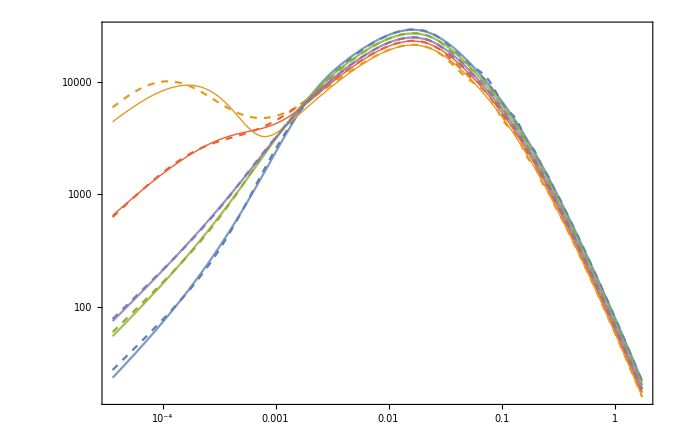

```mathematica
(* Graphic comparison *)
ListLogLogPlot[{PkE111.b4E221,PkE111n.b4E221n,PkE1105.b4E2205,PkE1105n.b4E2205n,PkE110.b4E221},Joined->True,PlotRange->All,PlotStyle->{Dashed},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#,Magnification->1.2]&)/@Style["E_{11} = 1, \\quad E_{22} = 1"],
(MaTeX[#,Magnification->1.2]&)/@Style["E_{11} = -1, \\quad E_{22} = -1"],
(MaTeX[#,Magnification->1.2]&)/@Style["E_{11} = 0.5, \\quad E_{22} = 0.5"],
(MaTeX[#,Magnification->1.2]&)/@Style["E_{11} = -0.5, \\quad E_{22} = -0.5"],
(MaTeX[#,Magnification->1.2]&)/@Style["E_{11} = 0, \\quad E_{22} = 1"]},
 LegendLayout->{"Row", 5},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.6,0.3}],AspectRatio->0.65,ImageSize->720];//Quiet
LogLogPlot[{P[k,w,k0,β,s]/.ParE111.b4E221[[2]],P[k,w,k0,β,s]/.ParE111n.b4E221n[[2]],P[k,w,k0,β,s]/.ParE1105.b4E2205[[2]],P[k,w,k0,β,s]/.ParE1105n.b4E2205n[[2]],P[k,w,k0,β,s]/.ParE110.b4E221[[2]]}//Evaluate,{k,PkE1105.b4E2205[[1,1]],PkE1105.b4E2205[[-1,1]]},PlotRange->All,PlotStyle->{Opacity[0.8],Thick},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];//Quiet
Show[{%%,%},PlotRange->All,ImageSize->680]//Quiet
```

# Matter Power Spectrum: HDES

## Data

```mathematica
(* Import datasets *)
HDES.b4Files="/Users/cosmology/hi_class_public/output/HDES/";
PkJc0.b4001=Import[HDES.b4Files<>"HDES_Jc_0.001_pk.dat","Data"][[5;;-1]]//Quiet;
PkJc0.b4003=Import[HDES.b4Files<>"HDES_Jc_0.003_pk.dat","Data"][[5;;-1]]//Quiet;
PkJc0.b4005=Import[HDES.b4Files<>"HDES_Jc_0.005_pk.dat","Data"][[5;;-1]]//Quiet;
PkJc0.b4008=Import[HDES.b4Files<>"HDES_Jc_0.008_pk.dat","Data"][[5;;-1]]//Quiet;
PkJc0.b401=Import[HDES.b4Files<>"HDES_Jc_0.01_pk.dat","Data"][[5;;-1]]//Quiet;
```

```mathematica
(* Power spectrum for wCDM from GA *)
Pw[k_,w_]:=(2.5239506940685576*^6 k^0.9645201679721765 (1+0.7106356245167889 w^3+1.8801896647991612 w^4+0.939216799027307 w^5))/(√(1+1395.2489187744666 k^1.4917653903428132+2.3729066856033597*^7 k^4.027553399922359+1.1994340119292421*^9 k^6.0600043498512886+7.611601220332279*^8 k^7.284778673036612))
ns=0.9619;
S[s_]:=3*10^6*(1+s) (* Shift factor *)
Psup[k_,s_]:=S[s]*k^ns; (* Primordial spectrum *)
Psub[k_,w_]:=Pw[k,w] (* wCDM P(k,w) *)
σ[k_,k0_,β_]:=1/(1+ⅇ^(-(k-k0)/β)); (* Transition function *)
P[k_,w_,k0_,β_,s_]:=(1-σ[k,k0,β])Psup[k,s]+σ[k,k0,β]*Psub[k,w] (* Total spectrum *)
```

## Comparison

```mathematica
(* Accuracy for each dataset *)
χ2P0.b4001[w_,k0_,β_,s_]:=Mean[Table[Abs[PkJc0.b4001⟦i,2⟧-P[PkJc0.b4001⟦i,1⟧,w,k0,β,s]]/(PkJc0.b4001⟦i,2⟧)*100,{i,1,Length[PkJc0.b4001]}]]
χ2P0.b4003[w_,k0_,β_,s_]:=Mean[Table[Abs[PkJc0.b4003⟦i,2⟧-P[PkJc0.b4003⟦i,1⟧,w,k0,β,s]]/(PkJc0.b4003⟦i,2⟧)*100,{i,1,Length[PkJc0.b4003]}]]
χ2P0.b4005[w_,k0_,β_,s_]:=Mean[Table[Abs[PkJc0.b4005⟦i,2⟧-P[PkJc0.b4005⟦i,1⟧,w,k0,β,s]]/(PkJc0.b4005⟦i,2⟧)*100,{i,1,Length[PkJc0.b4005]}]]
χ2P0.b4008[w_,k0_,β_,s_]:=Mean[Table[Abs[PkJc0.b4008⟦i,2⟧-P[PkJc0.b4008⟦i,1⟧,w,k0,β,s]]/(PkJc0.b4008⟦i,2⟧)*100,{i,1,Length[PkJc0.b4008]}]]
χ2P0.b401[w_,k0_,β_,s_]:=Mean[Table[Abs[PkJc0.b401⟦i,2⟧-P[PkJc0.b401⟦i,1⟧,w,k0,β,s]]/(PkJc0.b401⟦i,2⟧)*100,{i,1,Length[PkJc0.b401]}]]
```

```mathematica
(* Compute the most accurate set of parameters *)
Par0.b4001=FindMinimum[χ2P0.b4001[w,k0,β,s],{{w,0,2},{k0,0.0001,0.001},{β,0.0001,0.001},{s,0,1}}]
Par0.b4003=FindMinimum[χ2P0.b4003[w,k0,β,s],{{w,0,2},{k0,0.0001,0.001},{β,0.0001,0.001},{s,0,1}}]
Par0.b4005=FindMinimum[χ2P0.b4005[w,k0,β,s],{{w,0,2},{k0,0.0001,0.001},{β,0.0001,0.001},{s,0,1}}]
Par0.b4008=FindMinimum[χ2P0.b4008[w,k0,β,s],{{w,0,2},{k0,0.0001,0.001},{β,0.0001,0.001},{s,0,1}}]
Par0.b401=FindMinimum[χ2P0.b401[w,k0,β,s],{{w,0,2},{k0,0.0001,0.001},{β,0.0001,0.001},{s,0,1}}]
```

{1.51439,{w→0.542137,k0→8.10963×10^-6,β→0.00052467,s→0.0688498}}

{1.41932,{w→0.557605,k0→-0.00317628,β→0.00248,s→-0.12111}}

{1.46741,{w→0.57264,k0→0.00032235,β→0.0017408,s→-0.0341637}}

{1.49653,{w→0.595065,k0→0.00160229,β→0.00131829,s→-0.014953}}

{1.51694,{w→0.609387,k0→0.00193218,β→0.00107847,s→-0.00902124}}

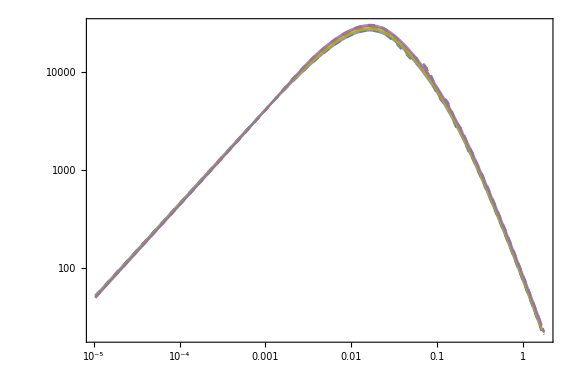

```mathematica
(* Graphic comparison *)
ListLogLogPlot[{PkJc0.b4001,PkJc0.b4003,PkJc0.b4005,PkJc0.b4008,PkJc0.b401},Joined->True,PlotRange->All,PlotStyle->{Dashed},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [ (\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{J}_c = 0.001"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{J}_c = 0.003"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{J}_c = 0.005"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{J}_c = 0.008"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\tilde{J}_c = 0.01"]},
 LegendLayout->{"Row", 3},LabelStyle->{Black,Bold,15},LegendMarkerSize->25,LegendFunction->Frame],{0.57,0.3}],AspectRatio->0.65,ImageSize->720];//Quiet
LogLogPlot[{P[k,w,k0,β,s]/.Par0.b4001[[2]],P[k,w,k0,β,s]/.Par0.b4003[[2]],P[k,w,k0,β,s]/.Par0.b4005[[2]],P[k,w,k0,β,s]/.Par0.b4008[[2]],P[k,w,k0,β,s]/.Par0.b401[[2]]}//Evaluate,{k,PkJc0.b4001[[1,1]],PkJc0.b4001[[-1,1]]},PlotRange->All,PlotStyle->{Opacity[0.8],Thick},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];//Quiet
Show[{%%,%},PlotRange->All,ImageSize->Large]//Quiet
```

# Sample Plot

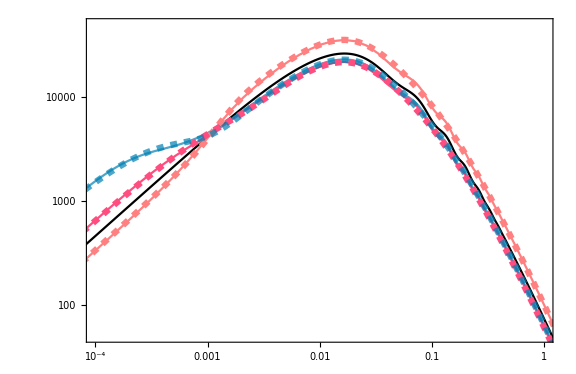

```mathematica
(* Plot some fits -> Excellent agreement *)
ListLogLogPlot[{PkΛCDM,PkB0.b45,PkM0.b45,PkE1105n.b4E2205n},Joined->True,PlotRange->All,PlotStyle->{Directive[Black],Directive[Pink,Opacity[1]],Directive[RGBColor[1,0.3,0.5],Opacity[1]],Directive[RGBColor[0,0.5,0.7],Opacity[0.7]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.8]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->18},AspectRatio->0.65,PlotLegends->Placed[LineLegend[{
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\Lambda\\text{CDM}"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_B = 0.1"],
(MaTeX[#, Magnification -> 1.2] &)/@Style["\\hat{\\alpha}_M = 0.5"],
(MaTeX[#,Magnification->1.2]&)/@Style["E_{ii} = -0.5"]},
 LegendLayout->{"Row", 2},LabelStyle->{Black,Bold,15},LegendMarkerSize->{30,25},LegendFunction->Frame],{0.5,0.22}],ImageSize->720];
LogLogPlot[{P[k,w,k0,β,s]/.ParαB0.b45[[2]],P[k,w,k0,β,s]/.ParαM0.b45[[2]],P[k,w,k0,β,s]/.ParE1105n.b4E2205n[[2]]}//Evaluate,{k,PkB0[[1,1]],PkB0[[-1,1]]},PlotRange->All,PlotStyle->{Directive[Pink,Dashed,Thickness[0.008],Opacity[1]],Directive[RGBColor[1,0.3,0.5],Dashed,Thickness[0.008],Opacity[1]],Directive[RGBColor[0,0.5,0.7],Dashed,Thickness[0.008],Opacity[0.7]]},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->1.3]&)/@{"k \\, [h \\,/ \\text{Mpc}]","P(k) \\, [(\\text{Mpc} / h)^3]"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->0.65,ImageSize->620];
Show[{%%,%},PlotRange->{{10^-4,1}//Log,{50,50000}//Log},ImageSize->Large]
```